# Представление вз-ия.

## Моменты по теореме вика

```mathematica
jw = {{0,-1},{1,0}};
mw[t_]:=({{am[t]}, {ap[t]}});
apf[t_]:=mw[t][[2,1]];
amf[t_]:=mw[t][[1,1]];
cw = ({{am2[t]-am[t]am[t], 1/2+n[t]-am[t]ap[t]}, {1/2+n[t]-am[t]ap[t], ap2[t]-ap[t]ap[t]}});
cf=cw(*-j/4.(Inverse[2*j.cw]+2*j.cw)*);
am2f[t_]:=cf[[1,1]]+amf[t]^2;
ap2f[t_]:=cf[[2,2]]+apf[t]^2;
nf[t_]:=cf[[1,2]]-1/2+amf[t]*apf[t];
dpm=nf[t]-apf[t]*amf[t];
dpp=ap2f[t]-apf[t]^2;
dmm=am2f[t]-amf[t]^2;
```

```mathematica
w1m0=apf[t]
```

ap[t]

```mathematica
w0m1=amf[t]
```

am[t]

```mathematica
w0m2=am2f[t](*a^2*)//FullSimplify
```

am2[t]

```mathematica
w2m0=ap2f[t](*a^(+2)*)//FullSimplify
```

ap2[t]

```mathematica
w1m1=nf[t](*n*)//FullSimplify
```

n[t]

```mathematica
w0m6=FullSimplify[90 dmm^3+90 dmm^2*amf[t]^2+15dmm*amf[t]^4+amf[t]^6](*a^6*)
```

-14 am[t]^6+105 am[t]^4 am2[t]-180 am[t]^2 am2[t]^2+90 am2[t]^3

```mathematica
w6m0=FullSimplify[90 dpp^3+90 dpp^2*apf[t]^2+15dpp*apf[t]^4+apf[t]^6](*a^(+6)*)
```

-14 ap[t]^6+105 ap[t]^4 ap2[t]-180 ap[t]^2 ap2[t]^2+90 ap2[t]^3

```mathematica
w1m5=FullSimplify[Expand[30dpm dmm dmm +30dpm dmm amf[t]^2+30dmm dmm apf[t]*amf[t]+5dpm amf[t]^4+10dmm apf[t] amf[t]^3+apf[t]*amf[t]^5]](*a^+a^5*)
```

4 am[t]^3 (4 am[t]^2-5 am2[t]) ap[t]+5 (am[t]^4-6 am[t]^2 am2[t]+6 am2[t]^2) n[t]

```mathematica
w5m1=FullSimplify[30dpm dpp dpp +30dpm dpp apf[t]^2+30dpp dpp amf[t]*apf[t]+5dpm apf[t]^4+10dpp amf[t] apf[t]^3+amf[t]*apf[t]^5](*a^(+5)a*)
```

4 am[t] (4 ap[t]^5-5 ap[t]^3 ap2[t])+5 (ap[t]^4-6 ap[t]^2 ap2[t]+6 ap2[t]^2) n[t]

```mathematica
w0m5=FullSimplify[30dmm*dmm*amf[t]+10dmm*amf[t]^3+amf[t]^5](*a^5*)
```

21 am[t]^5-50 am[t]^3 am2[t]+30 am[t] am2[t]^2

```mathematica
w5m0=FullSimplify[30dpp*dpp*apf[t]+10dpp*apf[t]^3+apf[t]^5](*a^(+5)*)
```

21 ap[t]^5-50 ap[t]^3 ap2[t]+30 ap[t] ap2[t]^2

```mathematica
w0m4=FullSimplify[6dmm*dmm+6dmm*amf[t]^2+amf[t]^4](*a^4*)
```

am[t]^4-6 am[t]^2 am2[t]+6 am2[t]^2

```mathematica
w4m0=FullSimplify[6dpp*dpp+6dpp*apf[t]^2+apf[t]^4](*a^(+4)*)
```

ap[t]^4-6 ap[t]^2 ap2[t]+6 ap2[t]^2

```mathematica
w1m2=FullSimplify[2dpm*amf[t]+apf[t]*dmm + apf[t] amf[t]^2](*fa^+a^2 f*)
```

-2 am[t]^2 ap[t]+am2[t] ap[t]+2 am[t] n[t]

```mathematica
w2m1=FullSimplify[2dpm*apf[t]+amf[t]*dpp+apf[t]^2 amf[t]](*fa^(+^2)af*)
```

am[t] (-2 ap[t]^2+ap2[t])+2 ap[t] n[t]

```mathematica
w2m3=FullSimplify[3dpp*dmm*amf[t]+6apf[t]*dpm*dmm+6amf[t]*dpm^2+dpp*amf[t]^3+6dpm*apf[t]*amf[t]^2+3dmm*apf[t]^2 amf[t]+apf[t]^2 amf[t]^3](*a^(+^2)a^3*)
```

am[t]^3 (6 ap[t]^2-2 ap2[t])-12 am[t]^2 ap[t] n[t]+6 am2[t] ap[t] n[t]+am[t] (3 am2[t] (-2 ap[t]^2+ap2[t])+6 n[t]^2)

```mathematica
w3m2=FullSimplify[3dmm*dpp*apf[t]+6amf[t]*dpm*dpp+6apf[t]*dpm^2+dmm*apf[t]^3+6dpm*amf[t]*apf[t]^2+3dpp*amf[t]^2 apf[t]+amf[t]^2 apf[t]^3](*a^(+^3)a^2*)
```

6 am[t]^2 (ap[t]^3-ap[t] ap2[t])+6 am[t] (-2 ap[t]^2+ap2[t]) n[t]+ap[t] (am2[t] (-2 ap[t]^2+3 ap2[t])+6 n[t]^2)

```mathematica
w2m2=FullSimplify[dpp*dmm+2 dpm^2+dpp*amf[t]^2+dmm*apf[t]^2+4dpm*apf[t]*amf[t]+apf[t]^2 amf[t]^2](*a^(+^2)a^2*)
```

-2 am[t]^2 ap[t]^2+am2[t] ap2[t]+2 n[t]^2

```mathematica
w3m3=FullSimplify[36 dpm^3+9dpp dmm dpm + 36 dpm^2 apf[t]amf[t]+9dmm dpp apf[t]amf[t]+9dpm apf[t]^2 amf[t]^2+3dpp apf[t] amf[t]^3+3dmm apf[t]^3 amf[t]+apf[t]^3 amf[t]^3](*a^(+3)a^3*)
```

am[t]^3 (-14 ap[t]^3+3 ap[t] ap2[t])+9 am[t]^2 (6 ap[t]^2-ap2[t]) n[t]+9 am2[t] (-ap[t]^2+ap2[t]) n[t]+36 n[t]^3+3 am[t] (am2[t] ap[t]^3-24 ap[t] n[t]^2)

```mathematica
w0m3=FullSimplify[amf[t]^3+3dmm*amf[t]](*a^3*)
```

-2 am[t]^3+3 am[t] am2[t]

```mathematica
w3m0=FullSimplify[apf[t]^3+3dpp*apf[t]](*(a^+)^3*)
```

-2 ap[t]^3+3 ap[t] ap2[t]

```mathematica
w1m3=FullSimplify[3dpm*dmm+3dpm*amf[t]^2+3apf[t]amf[t]*dmm+apf[t] amf[t]^3](*fa^+a^3 f*)
```

-2 am[t]^3 ap[t]+3 am2[t] n[t]

```mathematica
w3m1=FullSimplify[3dpm*dpp+3dpm*apf[t]^2+3amf[t]apf[t]*dpp+apf[t]^3 amf[t]](*fa^(+3)af*)
```

-2 am[t] ap[t]^3+3 ap2[t] n[t]

```mathematica
w2m4=FullSimplify[3dpp*dmm*dmm+12 dpm^2 dmm+3dpp*dmm*amf[t]^2+12 dpm^2 amf[t]^2+24dpm*dmm*apf[t]*amf[t]+6 dmm^2 apf[t]^2+dpp*amf[t]^4+8dpm*apf[t] amf[t]^3+6dmm*apf[t]^2 amf[t]^2+apf[t]^2 amf[t]^4](*a^(+^2)a^4*)
```

-3 am[t]^2 am2[t] (5 ap[t]^2+ap2[t])+am[t]^4 (16 ap[t]^2+ap2[t])-16 am[t]^3 ap[t] n[t]+3 am2[t] (am2[t] (ap[t]^2+ap2[t])+4 n[t]^2)

```mathematica
w4m2=FullSimplify[3dmm*dpp*dpp+12 dpm^2 dpp+3dmm*dpp*apf[t]^2+12 dpm^2 apf[t]^2+24dpm*dpp*amf[t]*apf[t]+6 dpp^2 amf[t]^2+dmm*apf[t]^4+8dpm*amf[t] apf[t]^3+6dpp*amf[t]^2 apf[t]^2+amf[t]^2 apf[t]^4](*a^(+^4)a^2*)
```

am[t]^2 (16 ap[t]^4-15 ap[t]^2 ap2[t]+3 ap2[t]^2)+am2[t] (ap[t]^4-3 ap[t]^2 ap2[t]+3 ap2[t]^2)-16 am[t] ap[t]^3 n[t]+12 ap2[t] n[t]^2

```mathematica
w1m4=FullSimplify[12dpm*dmm*amf[t]+6 dmm^2 apf[t]+4dpm*amf[t]^3+6dmm*apf[t]*amf[t]^2+apf[t]*amf[t]^4](*a^+a^4*)
```

3 (3 am[t]^4-6 am[t]^2 am2[t]+2 am2[t]^2) ap[t]+4 am[t] (-2 am[t]^2+3 am2[t]) n[t]

```mathematica
w4m1=FullSimplify[12dpm*dpp*apf[t]+6 dpp^2 amf[t]+4dpm*apf[t]^3+6dpp*amf[t]*apf[t]^2+amf[t]*apf[t]^4](*a^(+4)a*)
```

3 am[t] (3 ap[t]^4-6 ap[t]^2 ap2[t]+2 ap2[t]^2)+4 ap[t] (-2 ap[t]^2+3 ap2[t]) n[t]

## Коэфициенты при операторах

```mathematica
j={{0,-1,0,0},{1,0,0,0},{0,0,0,-1},{0,0,1,0}}; (*Матрица Subscript[J, 2], равная прямой суммы j*)
h={{0,-Δ},{-Δ,0}}; (*Матрица квадратичной части гамильтониана H*)
g={{0,γ/2},{0,0}}; (*Матрица Γ диссипативной части*)
e={{0,1},{1,0}};
f={{-F},{F},{-F},{F}}; (*матрица линейной части гамильтониана*)
i=IdentityMatrix[4];
ll={{-I*h-(g+Transpose[g])/2,g.e},{e.Transpose[g],e.(I*h-(g+Transpose[g])/2).e}}//MatrixForm (*Блочная матрица Subscript[L, t], участвующая в уравнении 1.83 диссертации*)
l={{0,-γ/4+I*Δ,γ/2,0},{-γ/4+ⅈ Δ,0,0,0},{γ/2,0,0,-γ/4-ⅈ Δ},{0,0,-γ/4-I*Δ,0}}(*Матрица Subscript[L, t], участвующая в уравнении 1.83 диссертации*)
l//MatrixForm
e.h.e//MatrixForm
h//MatrixForm
```

((0 | -γ/4+ⅈ Δ
-γ/4+ⅈ Δ | 0) | (γ/2 | 0
0 | 0)
(γ/2 | 0
0 | 0) | (0 | -γ/4-ⅈ Δ
-γ/4-ⅈ Δ | 0))

{{0,-γ/4+ⅈ Δ,γ/2,0},{-γ/4+ⅈ Δ,0,0,0},{γ/2,0,0,-γ/4-ⅈ Δ},{0,0,-γ/4-ⅈ Δ,0}}

(0 | -γ/4+ⅈ Δ | γ/2 | 0
-γ/4+ⅈ Δ | 0 | 0 | 0
γ/2 | 0 | 0 | -γ/4-ⅈ Δ
0 | 0 | -γ/4-ⅈ Δ | 0)

(0 | -Δ
-Δ | 0)

(0 | -Δ
-Δ | 0)

```mathematica
intrep[F_,t_]:=Inverse[l].MatrixExp[-l.j*t].l.{{al0},{alp0},{arp0},{ar0}} + Inverse[l].(MatrixExp[-l.j*t]-i).{{-F},{F},{-F},{F}} (*Решение уравнения 1.83*)
```

```mathematica
Collect[intrep[F,t],{F,al0,ar0,alp0,arp0},FullSimplify]//MatrixForm
```

(al0 ⅇ^(-(t γ)/4+ⅈ t Δ)+((4-4 ⅇ^(-(t γ)/4+ⅈ t Δ)) F)/(γ-4 ⅈ Δ)
alp0 ⅇ^(1/4 t (γ-4 ⅈ Δ))+((4-4 ⅇ^(-1/4 t (γ+4 ⅈ Δ))) F)/(γ+4 ⅈ Δ)-2 arp0 ⅇ^(-ⅈ t Δ) Sinh[(t γ)/4]
arp0 ⅇ^(-1/4 t (γ+4 ⅈ Δ))+((4-4 ⅇ^(-1/4 t (γ+4 ⅈ Δ))) F)/(γ+4 ⅈ Δ)
ar0 ⅇ^(1/4 t (γ+4 ⅈ Δ))+((4-4 ⅇ^(-(t γ)/4+ⅈ t Δ)) F)/(γ-4 ⅈ Δ)-2 al0 ⅇ^(ⅈ t Δ) Sinh[(t γ)/4])

```mathematica
Collect[intrep[F,t][[1]],{F,al0},FullSimplify]
Collect[intrep[F,t][[2]],{F,ar0,alp0},FullSimplify]
Collect[intrep[F,t][[3]],{F,ar0},FullSimplify]
Collect[intrep[F,t][[4]],{F,al0,arp0},FullSimplify]
```

{al0 ⅇ^(-(t γ)/4+ⅈ t Δ)+((4-4 ⅇ^(-(t γ)/4+ⅈ t Δ)) F)/(γ-4 ⅈ Δ)}

{alp0 ⅇ^(1/4 t (γ-4 ⅈ Δ))+((4-4 ⅇ^(-1/4 t (γ+4 ⅈ Δ))) F)/(γ+4 ⅈ Δ)-2 arp0 ⅇ^(-ⅈ t Δ) Sinh[(t γ)/4]}

{arp0 ⅇ^(-1/4 t (γ+4 ⅈ Δ))+((4-4 ⅇ^(-1/4 t (γ+4 ⅈ Δ))) F)/(γ+4 ⅈ Δ)}

{ar0 ⅇ^(1/4 t (γ+4 ⅈ Δ))+((4-4 ⅇ^(-(t γ)/4+ⅈ t Δ)) F)/(γ-4 ⅈ Δ)-2 al0 ⅇ^(ⅈ t Δ) Sinh[(t γ)/4]}

```mathematica
Clear[j,i]
```

```mathematica
a1[t_]:=ⅇ^(-(t γ)/4+ⅈ t Δ);
b1[t_]:=((4-4 ⅇ^(-(t γ)/4+ⅈ t Δ)) F)/(γ-4 ⅈ Δ);
a21[t_]:=ⅇ^(1/4 t (γ-4 ⅈ Δ));
a22[t_]:=-2 ⅇ^(-ⅈ t Δ) Sinh[(t γ)/4];
b2[t_]:=((4-4 ⅇ^(-1/4 t (γ+4 ⅈ Δ))) F)/(γ+4 ⅈ Δ);
a3[t_]:=ⅇ^(-1/4 t (γ+4 ⅈ Δ));
b3[t_]:=((4-4 ⅇ^(-1/4 t (γ+4 ⅈ Δ))) F)/(γ+4 ⅈ Δ);
a41[t_]:=ⅇ^(1/4 t (γ+4 ⅈ Δ));
a42[t_]:=-2  ⅇ^(ⅈ t Δ) Sinh[(t γ)/4];
b4[t_]:=((4-4 ⅇ^(-(t γ)/4+ⅈ t Δ)) F)/(γ-4 ⅈ Δ);
cc1[n_,m_,t_]:=m(m-1)-n(n-1)
cc2[n_,m_,t_]:=2(m-n)ⅇ^(-γ/2 t)
cc3[n_,m_,t_]:=2 a1[t]^2 b2[t] a21[t] m - 4b3[t] a3[t] a41[t] n(a41[t] + a42[t])
cc4[n_,m_,t_]:=2 a1[t]^2 b2[t] a21[t] + 2(a1[t]^2 b2[t] a22[t] - b3[t] a3[t] a42[t]^2)-2b3[t] a3[t] a41[t](a41[t] + 2a42[t])
cc5[n_,m_,t_]:=2b1[t] a1[t] a21[t]^2 m(m-1)
cc6[n_,m_,t_]:=-2b3[t] a3[t] a41[t]^2 n(n-1)
cc7[n_,m_,t_]:=4b1[t] a1[t] a21[t] m(a21[t] + a22[t])-2 a3[t]^2 b4[t] a41[t] n
cc8[n_,m_,t_]:=2b1[t] a1[t] a21[t](a21[t] + 2a22[t])-2 a3[t]^2 b4[t] a41[t] + 2(b1[t] a1[t] a22[t]^2-a3[t]^2 b4[t] a42[t])
```

```mathematica
z=s;
x=2;
y=0;
FullSimplify[cc1[x,y,z]]
FullSimplify[cc2[x,y,z]]
FullSimplify[cc3[x,y,z]]
FullSimplify[cc4[x,y,z]]
FullSimplify[cc5[x,y,z]]
FullSimplify[cc6[x,y,z]]
FullSimplify[cc7[x,y,z]]
FullSimplify[cc8[x,y,z]]
```

-2

-4 ⅇ^(-(s γ)/2)

-(32 ⅇ^(-(s γ)/2) (-1+ⅇ^(1/4 s (γ+4 ⅈ Δ))) F)/(γ+4 ⅈ Δ)

0

0

-(16 (-1+ⅇ^(1/4 s (γ+4 ⅈ Δ))) F)/(γ+4 ⅈ Δ)

-(16 ⅇ^(-(s γ)/2) (-1+ⅇ^(1/4 s (γ-4 ⅈ Δ))) F)/(γ-4 ⅈ Δ)

0

## Первые и вторые слагаемые (посчитанные)

```mathematica
(*filedir1 ="E:\\Work\\Wolfram\\Промежуточные\\1-ый режим\\"; 
DeleteFile[{FileNameJoin[{filedir1,"ch15s.m"}],FileNameJoin[{filedir1,"ch15t.m"}]}];
DeleteFile[{FileNameJoin[{filedir1,"ch14s.m"}],FileNameJoin[{filedir1,"ch14t.m"}]}];
DeleteFile[{FileNameJoin[{filedir1,"ch13s.m"}],FileNameJoin[{filedir1,"ch13t.m"}]}];
DeleteFile[{FileNameJoin[{filedir1,"ch12s.m"}],FileNameJoin[{filedir1,"ch12t.m"}]}];
DeleteFile[{FileNameJoin[{filedir1,"ch11s.m"}],FileNameJoin[{filedir1,"ch11t.m"}]}];
DeleteFile[FileNameJoin[{filedir1,"ch25.m"}]];
DeleteFile[FileNameJoin[{filedir1,"ch24.m"}]];
DeleteFile[FileNameJoin[{filedir1,"ch23.m"}]];
DeleteFile[FileNameJoin[{filedir1,"ch22.m"}]];
DeleteFile[FileNameJoin[{filedir1,"ch21.m"}]];*)
```

DeleteFile::fdnfnd: Directory or file "E:\Work\Wolfram\Промежуточные\1-ый режим\ch15s.m" not found.

DeleteFile::fdnfnd: Directory or file "E:\Work\Wolfram\Промежуточные\1-ый режим\ch14s.m" not found.

DeleteFile::fdnfnd: Directory or file "E:\Work\Wolfram\Промежуточные\1-ый режим\ch13s.m" not found.

DeleteFile::fdnfnd: Directory or file "E:\Work\Wolfram\Промежуточные\1-ый режим\ch12s.m" not found.

DeleteFile::fdnfnd: Directory or file "E:\Work\Wolfram\Промежуточные\1-ый режим\ch11s.m" not found.

DeleteFile::fdnfnd: Directory or file "E:\Work\Wolfram\Промежуточные\1-ый режим\ch24.m" not found.

DeleteFile::fdnfnd: Directory or file "E:\Work\Wolfram\Промежуточные\1-ый режим\ch23.m" not found.

DeleteFile::fdnfnd: Directory or file "E:\Work\Wolfram\Промежуточные\1-ый режим\ch22.m" not found.

DeleteFile::fdnfnd: Directory or file "E:\Work\Wolfram\Промежуточные\1-ый режим\ch21.m" not found.

```mathematica
(*ch15[s_]:=-ⅈ*χ/2(cc1[2,0,s]*w2m0+cc2[2,0,s]*w3m1+cc3[2,0,s]*w2m1+cc6[2,0,s]*w1m0+cc7[2,0,s]*w3m0);
ch15s=Integrate[ch15[s],{s,0,t}];
ch15t=ch15[t];
tempfile1s=FileNameJoin[{filedir1,"ch15s.m"}];
tempfile1t=FileNameJoin[{filedir1,"ch15t.m"}];
Save[tempfile1s,ch15s]
Save[tempfile1t,ch15t]*)
```

```mathematica
(*ch14[s_]:=-ⅈ*χ/2(cc1[0,2,s]*w0m2+cc2[0,2,s]*w1m3+cc3[0,2,s]*w0m3+cc5[0,2,s]*w0m1+cc7[0,2,s]*w1m2);
ch14s=Integrate[ch14[s],{s,0,t}];
ch14t=ch14[t];
tempfile1s=FileNameJoin[{filedir1,"ch14s.m"}];
tempfile1t=FileNameJoin[{filedir1,"ch14t.m"}];
Save[tempfile1s,ch14s]
Save[tempfile1t,ch14t]*)
```

```mathematica
(*ch13[s_]:=-ⅈ*χ/2(cc3[1,1,s]*w1m2+cc7[1,1,s]*w2m1);
ch13s=Integrate[ch13[s],{s,0,t}];
ch13t=ch13[t];
tempfile1s=FileNameJoin[{filedir1,"ch13s.m"}];
tempfile1t=FileNameJoin[{filedir1,"ch13t.m"}];
Save[tempfile1s,ch13s]
Save[tempfile1t,ch13t]*)
```

```mathematica
(*ch12[s_]:=-ⅈ*χ/2(cc2[1,0,s]*w2m1+cc3[1,0,s]*w1m1+cc7[1,0,s]*w2m0);
ch12s=Integrate[ch12[s],{s,0,t}];
ch12t=ch12[t];
tempfile1s=FileNameJoin[{filedir1,"ch12s.m"}];
tempfile1t=FileNameJoin[{filedir1,"ch12t.m"}];
Save[tempfile1s,ch12s]
Save[tempfile1t,ch12t]*)
```

```mathematica
(*ch11[s_]:=-ⅈ*χ/2(cc2[0,1,s]*w1m2+cc3[0,1,s]*w0m2+cc7[0,1,s]*w1m1);
ch11s=Integrate[ch11[s],{s,0,t}];
ch11t=ch11[t];
tempfile1s=FileNameJoin[{filedir1,"ch11s.m"}];
tempfile1t=FileNameJoin[{filedir1,"ch11t.m"}];
Save[tempfile1s,ch11s]
Save[tempfile1t,ch11t]*)
```

```mathematica
(*ch25=Integrate[-χ^2/4(cc1[2,0,t](cc1[2,0,s]*w2m0+cc2[2,0,s]*w3m1+cc3[2,0,s]*w2m1+cc6[2,0,s]*w1m0+cc7[2,0,s]*w3m0)+
cc2[2,0,t](cc1[3,1,s]*w3m1+cc2[3,1,s]*w4m2+cc3[3,1,s]*w3m2+cc6[3,1,s]*w2m1+cc7[3,1,s]*w4m1)+
cc3[2,0,t](cc1[2,1,s]*w2m1+cc2[2,1,s]*w3m1+cc3[2,1,s]*w2m2+cc6[2,1,s]*w1m1)+
cc6[2,0,t](cc2[1,0,s]*w2m1+cc3[1,0,s]*w1m1+cc7[1,0,s]*w2m0)+
cc7[2,0,t](cc1[3,0,s]*w3m0+cc2[3,0,s]*w4m1+cc3[3,0,s]*w3m1+cc6[3,0,s]*w2m0+cc7[3,0,s]*w4m0)),{s,0,t}];
tempfile1=FileNameJoin[{filedir1,"ch25.m"}];
Save[tempfile1,ch25]*)
```

```mathematica
(*ch24=Integrate[-χ^2/4(cc1[0,2,t](cc1[0,2,s]*w0m2+cc2[0,2,s]*w1m3+cc3[0,2,s]*w0m3+cc5[0,2,s]*w0m1+cc7[0,2,s]*w1m2)+
cc2[0,2,t](cc1[1,3,s]*w1m3+cc2[1,3,s]*w2m4+cc3[1,3,s]*w1m4+cc5[1,3,s]*w1m2+cc7[1,3,s]*w2m3)+
cc3[0,2,t](cc1[0,3,s]*w0m3+cc2[0,3,s]*w1m4+cc3[0,3,s]*w0m4+cc5[0,3,s]*w0m2+cc7[0,3,s]*w1m3)+
cc5[0,2,t](cc2[0,1,s]*w1m2+cc3[0,1,s]*w0m2+cc7[0,1,s]*w1m1)+
cc7[0,2,t](cc1[1,2,s]*w1m2+cc2[1,2,s]*w2m3+cc5[1,2,s]*w1m1+cc7[1,2,s]*w2m2)),{s,0,t}];
tempfile1=FileNameJoin[{filedir1,"ch24.m"}];
Save[tempfile1,ch24]*)
```

```mathematica
(*ch23=Integrate[-χ^2/4(cc3[1,1,t](cc1[1,2,s]*w1m2+cc2[1,2,s]*w2m3+cc5[1,2,s]*w1m1+cc7[1,2,s]*w2m2)+
cc7[1,1,t](cc1[2,1,s]*w2m1+cc2[2,1,s]*w3m2+cc3[2,1,s]*w2m2+cc6[2,1,s]*w1m1)),{s,0,t}];
tempfile1=FileNameJoin[{filedir1,"ch23.m"}];
Save[tempfile1,ch23]*)
```

```mathematica
(*ch22=Integrate[-χ^2/4(cc2[1,0,t](cc1[2,1,s]*w2m1+cc2[2,1,s]*w3m2+cc3[2,1,s]*w2m2+cc6[2,1,s]*w1m1)+
cc3[1,0,t](cc3[1,1,s]*w1m2+cc7[1,1,s]*w2m1)+
cc7[1,0,t](cc1[2,0,s]*w2m0+cc2[2,0,s]*w3m1+cc3[2,0,s]*w2m1+cc6[2,0,s]*w1m0+cc7[2,0,s]*w3m0)),{s,0,t}];
tempfile1=FileNameJoin[{filedir1,"ch22.m"}];
Save[tempfile1,ch22]*)
```

```mathematica
(*ch21=Integrate[-χ^2/4(cc2[0,1,t](cc1[1,2,s]*w1m2+cc2[1,2,s]*w2m3+cc5[1,2,s]*w1m1+cc7[1,2,s]*w2m2)+
cc3[0,1,t](cc1[0,2,s]*w0m2+cc2[0,2,s]*w1m3+cc3[0,2,s]*w0m3+cc5[0,2,s]*w0m1+cc7[0,2,s]*w1m2)+
cc7[0,1,t](cc3[1,1,s]*w1m2+cc7[1,1,s]*w2m1)),{s,0,t}];
tempfile1=FileNameJoin[{filedir1,"ch21.m"}];
Save[tempfile1,ch21]*)
```

## Выгрузка после сохранения

```mathematica
filedir2 ="E:\\Work\\Wolfram\\Промежуточные\\1-ый режим\\";
```

```mathematica
ch15s=Get[FileNameJoin[{filedir2,"ch15s.m"}]];
ch15t=Get[FileNameJoin[{filedir2,"ch15t.m"}]];
ch14s=Get[FileNameJoin[{filedir2,"ch14s.m"}]];
ch14t=Get[FileNameJoin[{filedir2,"ch14t.m"}]];
ch13s=Get[FileNameJoin[{filedir2,"ch13s.m"}]];
ch13t=Get[FileNameJoin[{filedir2,"ch13t.m"}]];
ch12s=Get[FileNameJoin[{filedir2,"ch12s.m"}]];
ch12t=Get[FileNameJoin[{filedir2,"ch12t.m"}]];
ch11s=Get[FileNameJoin[{filedir2,"ch11s.m"}]];
ch11t=Get[FileNameJoin[{filedir2,"ch11t.m"}]];
```

```mathematica
ch25=Get[FileNameJoin[{filedir2,"ch25.m"}]];
ch24=Get[FileNameJoin[{filedir2,"ch24.m"}]];
ch23=Get[FileNameJoin[{filedir2,"ch23.m"}]];
ch22=Get[FileNameJoin[{filedir2,"ch22.m"}]];
ch21=Get[FileNameJoin[{filedir2,"ch21.m"}]];
```

# Матрицы из 3-го слагаемого

## Матрицы

```mathematica
j = {{0,-1},{1,0}};
i=IdentityMatrix[2];
c = ({{am2[t]-am[t]am[t], 1/2+n[t]-am[t]ap[t]}, {1/2+n[t]-am[t]ap[t], ap2[t]-ap[t]ap[t]}});
m=({{am[t]}, {ap[t]}});
```

```mathematica
k = FullSimplify[2MatrixFunction[ArcCoth,-2*Inverse[j].c].Inverse[j]];
g=-k.m;
```

```mathematica
(*detmatr=FullSimplify[Det[-2Inverse[2Inverse[j].c+i]]];*)
```

```mathematica
M[x_]:=Inverse[c-j/2].D[c,x].Inverse[c+j/2]//FullSimplify;
G[x_]:=(i+2Inverse[2*Inverse[j].c-i]).D[Inverse[c+j/2].m,x]//FullSimplify;
c0[x_]:=-Transpose[m].Inverse[2*Inverse[j].c-i].D[Inverse[c+j/2].m,x]+1/2 D[Transpose[m].(Inverse[2*Inverse[j].c-i]-Inverse[2*Inverse[j].c+i]-k.j).Inverse[j].m,x]+(D[1/2 Log[Det[2Inverse[2Inverse[j].c+i]]],x]+1/2 D[Transpose[m].k.m,x]);
```

```mathematica
tM[x_]:=1/2(i+2Inverse[2Inverse[j].c-i]).M[x].j.(i-2Inverse[2Inverse[j].c+i]).Inverse[j]
tG[x_]:=2(i+2Inverse[2Inverse[j].c-i]).M[x].j.Inverse[2Inverse[j].c+i].Inverse[j].m+(i+2Inverse[2Inverse[j].c-i]).G[x]
tc0[x_]:=2(-Transpose[m].Inverse[2Inverse[j].c-i].M[x]+Transpose[G[x]]).j.Inverse[2Inverse[j].c+i].Inverse[j].m+c0[x]
```

## Полные матрицы (сумма из-за скалярного произведения)

```mathematica
Mf=ch11t*M[am[t]]+ch12t*M[ap[t]]+ch13t*M[n[t]]+ch14t*M[am2[t]]+ch15t*M[ap2[t]];
Gf=ch11t*G[am[t]]+ch12t*G[ap[t]]+ch13t*G[n[t]]+ch14t*G[am2[t]]+ch15t*G[ap2[t]];
c0f=ch11t*c0[am[t]]+ch12t*c0[ap[t]]+ch13t*c0[n[t]]+ch14t*c0[am2[t]]+ch15t*c0[ap2[t]];
```

```mathematica
tMf=ch11s*tM[am[t]]+ch12s*tM[ap[t]]+ch13s*tM[n[t]]+ch14s*tM[am2[t]]+ch15s*tM[ap2[t]];
tGf=ch11s*tG[am[t]]+ch12s*tG[ap[t]]+ch13s*tG[n[t]]+ch14s*tG[am2[t]]+ch15s*tG[ap2[t]];
tc0f=ch11s*tc0[am[t]]+ch12s*tc0[ap[t]]+ch13s*tc0[n[t]]+ch14s*tc0[am2[t]]+ch15s*tc0[ap2[t]];
```

## Коэффициенты перед операторами

```mathematica
Q=(Mf*tc0f[[1,1]])/2+c0f[[1,1]]*tMf;
```

```mathematica
(*a^4*)
cho1=1/2 Mf[[1,1]]tMf[[1,1]];
```

```mathematica
(*a^(+4)*)
cho2=1/2 Mf[[2,2]]tMf[[2,2]];
```

```mathematica
(*a^2*)
cho3=Mf[[1,1]](tMf[[1,2]]+tMf[[2,1]])+1/2(Mf[[1,1]]tMf[[1,2]]+tMf[[1,1]]Mf[[1,2]])+Q[[1,1]]+Gf[[1,1]]*tGf[[1,1]];
(*a^(+2)*)
cho4=tMf[[2,2]](Mf[[1,2]]+Mf[[2,1]])+1/2(tMf[[1,2]]Mf[[2,2]]+Mf[[1,2]]tMf[[2,2]])+Q[[2,2]]+Gf[[2,1]]*tGf[[2,1]];
```

```mathematica
(*a^+a^3*)
cho5=1/2 Mf[[1,1]](tMf[[1,2]]+tMf[[2,1]])+1/2(Mf[[1,2]]+Mf[[2,1]])tMf[[1,1]];
```

```mathematica
(*a^(+3)a*)
cho6=1/2 Mf[[2,2]](tMf[[1,2]]+tMf[[2,1]])+1/2(Mf[[1,2]]+Mf[[2,1]])tMf[[2,2]];
```

```mathematica
(*a^(+2)a^2*)
cho7=1/2 Mf[[1,1]]tMf[[2,2]]+1/2(Mf[[1,2]]+Mf[[2,1]])(tMf[[1,2]]+tMf[[2,1]])+1/2 Mf[[2,2]]tMf[[1,1]];
```

```mathematica
(*n*)
cho8=2Mf[[1,1]]tMf[[2,2]]+1/2(Mf[[1,2]]+Mf[[2,1]])(tMf[[1,2]]+tMf[[2,1]])+1/2(Mf[[1,2]]+Mf[[2,1]])tMf[[1,2]]+1/2(tMf[[1,2]]+tMf[[2,1]])Mf[[1,2]]+(Q[[1,2]]+Q[[2,1]])+(Gf[[2,1]]tGf[[1,1]]+Gf[[1,1]]tGf[[2,1]]);
```

```mathematica
(*a^3*)
cho9=1/2 Mf[[1,1]]tGf[[1,1]]+Gf[[1,1]]tMf[[1,1]];
```

```mathematica
(*a^(+3)*)
cho10=1/2 Mf[[2,2]]tGf[[2,1]]+Gf[[2,1]]tMf[[2,2]];
```

```mathematica
(*a^+a^2*)
cho11=1/2 Mf[[1,1]]tGf[[2,1]]+1/2(Mf[[1,2]]+Mf[[2,1]])tGf[[1,1]]+Gf[[1,1]](tMf[[1,2]]+tMf[[2,1]])+Gf[[2,1]]tMf[[1,1]];
```

```mathematica
(*a^(+2)a*)
cho12=1/2 Mf[[2,2]]tGf[[1,1]]+1/2(Mf[[1,2]]+Mf[[2,1]])tGf[[2,1]]+Gf[[2,1]](tMf[[1,2]]+tMf[[2,1]])+Gf[[1,1]]tMf[[2,2]];
```

```mathematica
(*a*)
cho13=Mf[[1,1]]tGf[[2,1]]+1/2 Mf[[1,2]]tGf[[1,1]]+Gf[[1,1]](tMf[[1,2]]+tMf[[2,1]])+Gf[[1,1]]tMf[[1,2]]+Gf[[1,1]]tc0f[[1,1]]+tGf[[1,1]]c0f[[1,1]];
```

```mathematica
(*a^+*)
cho14=2tMf[[2,2]]Gf[[1,1]]+1/2 Mf[[1,2]]tGf[[2,1]]+1/2 tGf[[2,1]](Mf[[1,2]]+Mf[[2,1]])+Gf[[2,1]]tMf[[1,2]]+Gf[[2,1]]tc0f[[1,1]]+tGf[[2,1]]c0f[[1,1]];
```

```mathematica
(*0*)
cho15=Mf[[1,1]]tMf[[2,2]]+1/2 Mf[[1,2]]tMf[[1,2]]+Q[[1,2]]+Gf[[1,1]]tGf[[2,1]]+c0f[[1,1]]tc0f[[1,1]];
```

## 3-ее слагаемое

## перенормированный вик

```mathematica
jw = {{0,-1},{1,0}};
mw[t_]:=2({{am[t]}, {ap[t]}});
apf[t_]:=mw[t][[2,1]];
amf[t_]:=mw[t][[1,1]];
cw = ({{am2[t]-am[t]am[t], 1/2+n[t]-am[t]ap[t]}, {1/2+n[t]-am[t]ap[t], ap2[t]-ap[t]ap[t]}});
cf=(-jw/4).(Inverse[2*jw.cw]+2*jw.cw);
am2f[t_]:=cf[[1,1]]+amf[t]^2;
ap2f[t_]:=cf[[2,2]]+apf[t]^2;
nf[t_]:=cf[[1,2]]-1/2+amf[t]*apf[t];
dpm=nf[t]-apf[t]*amf[t];
dpp=ap2f[t]-apf[t]^2;
dmm=am2f[t]-amf[t]^2;
```

```mathematica
w1m0=apf[t]
```

2 ap[t]

```mathematica
w0m1=amf[t]
```

2 am[t]

```mathematica
w0m2=am2f[t](*a^2*)//FullSimplify
```

1/2 (7 am[t]^2+am2[t]+(-am[t]^2+am2[t])/(4 am2[t] (ap[t]^2-ap2[t])+4 am[t]^2 ap2[t]-4 am[t] ap[t] (1+2 n[t])+(1+2 n[t])^2))

```mathematica
w2m0=ap2f[t](*a^(+2)*)//FullSimplify
```

1/2 (7 ap[t]^2+ap2[t]+(-ap[t]^2+ap2[t])/(4 am2[t] (ap[t]^2-ap2[t])+4 am[t]^2 ap2[t]-4 am[t] ap[t] (1+2 n[t])+(1+2 n[t])^2))

```mathematica
w1m1=nf[t](*n*)//FullSimplify
```

1/2 (-1/2+7 am[t] ap[t]+n[t]+(1-2 am[t] ap[t]+2 n[t])/(8 am2[t] (ap[t]^2-ap2[t])+8 am[t]^2 ap2[t]-8 am[t] ap[t] (1+2 n[t])+2 (1+2 n[t])^2))

```mathematica
w0m6=FullSimplify[90 dmm^3+90 dmm^2*amf[t]^2+15dmm*amf[t]^4+amf[t]^6](*a^6*)
```

64 am[t]^6+120 am[t]^4 (-am[t]^2+am2[t]) (1+1/(4 am2[t] (ap[t]^2-ap2[t])+4 am[t]^2 ap2[t]-4 am[t] ap[t] (1+2 n[t])+(1+2 n[t])^2))+90 am[t]^2 (am[t]^2-am2[t])^2 (1+1/(4 am2[t] (ap[t]^2-ap2[t])+4 am[t]^2 ap2[t]-4 am[t] ap[t] (1+2 n[t])+(1+2 n[t])^2))^2+45/4 (-am[t]^2+am2[t])^3 (1+1/(4 am2[t] (ap[t]^2-ap2[t])+4 am[t]^2 ap2[t]-4 am[t] ap[t] (1+2 n[t])+(1+2 n[t])^2))^3

```mathematica
w6m0=FullSimplify[90 dpp^3+90 dpp^2*apf[t]^2+15dpp*apf[t]^4+apf[t]^6](*a^(+6)*)
```

64 ap[t]^6+120 ap[t]^4 (ap[t]^2-ap2[t]) (-1-1/(4 am2[t] (ap[t]^2-ap2[t])+4 am[t]^2 ap2[t]-4 am[t] ap[t] (1+2 n[t])+(1+2 n[t])^2))+90 ap[t]^2 (ap[t]^2-ap2[t])^2 (1+1/(4 am2[t] (ap[t]^2-ap2[t])+4 am[t]^2 ap2[t]-4 am[t] ap[t] (1+2 n[t])+(1+2 n[t])^2))^2-45/4 (ap[t]^2-ap2[t])^3 (1+1/(4 am2[t] (ap[t]^2-ap2[t])+4 am[t]^2 ap2[t]-4 am[t] ap[t] (1+2 n[t])+(1+2 n[t])^2))^3

```mathematica
w1m5=FullSimplify[Expand[30dpm dmm dmm +30dpm dmm amf[t]^2+30dmm dmm apf[t]*amf[t]+5dpm amf[t]^4+10dmm apf[t] amf[t]^3+apf[t]*amf[t]^5]](*a^+a^5*)
```

1/8 (-55 am[t]^4-90 am[t]^2 am2[t]-15 am2[t]^2+2 am[t]^5 ap[t]-20 am[t]^3 am2[t] ap[t]+210 am[t] am2[t]^2 ap[t]+10 (11 am[t]^4+18 am[t]^2 am2[t]+3 am2[t]^2) n[t]-(15 (am[t]^2-am2[t])^2 (-1+2 am[t] ap[t]-2 n[t]))/((4 am2[t] (ap[t]^2-ap2[t])+4 am[t]^2 ap2[t]-4 am[t] ap[t] (1+2 n[t])+(1+2 n[t])^2)^3)+(5 (-18 am[t]^5 ap[t]-124 am[t]^3 am2[t] ap[t]+78 am[t] am2[t]^2 ap[t]+am[t]^4 (29-14 n[t])+3 am2[t]^2 (-1+6 n[t])+6 am[t]^2 am2[t] (1+10 n[t])))/(4 am2[t] (ap[t]^2-ap2[t])+4 am[t]^2 ap2[t]-4 am[t] ap[t] (1+2 n[t])+(1+2 n[t])^2)+(15 (am[t]^2-am2[t]) (26 am[t]^3 ap[t]-10 am[t] am2[t] ap[t]-am2[t] (1+6 n[t])-am[t]^2 (7+10 n[t])))/((4 am2[t] (ap[t]^2-ap2[t])+4 am[t]^2 ap2[t]-4 am[t] ap[t] (1+2 n[t])+(1+2 n[t])^2)^2))

```mathematica
w5m1=FullSimplify[30dpm dpp dpp +30dpm dpp apf[t]^2+30dpp dpp amf[t]*apf[t]+5dpm apf[t]^4+10dpp amf[t] apf[t]^3+amf[t]*apf[t]^5](*a^(+5)a*)
```

1/8 (-55 ap[t]^4+2 am[t] ap[t]^5-90 ap[t]^2 ap2[t]-20 am[t] ap[t]^3 ap2[t]-15 ap2[t]^2+210 am[t] ap[t] ap2[t]^2+10 (11 ap[t]^4+18 ap[t]^2 ap2[t]+3 ap2[t]^2) n[t]-(15 (ap[t]^2-ap2[t])^2 (-1+2 am[t] ap[t]-2 n[t]))/((4 am2[t] (ap[t]^2-ap2[t])+4 am[t]^2 ap2[t]-4 am[t] ap[t] (1+2 n[t])+(1+2 n[t])^2)^3)+(15 (ap[t]^2-ap2[t]) (26 am[t] ap[t]^3-10 am[t] ap[t] ap2[t]-ap2[t] (1+6 n[t])-ap[t]^2 (7+10 n[t])))/((4 am2[t] (ap[t]^2-ap2[t])+4 am[t]^2 ap2[t]-4 am[t] ap[t] (1+2 n[t])+(1+2 n[t])^2)^2)-(5 (18 am[t] ap[t]^5+124 am[t] ap[t]^3 ap2[t]-78 am[t] ap[t] ap2[t]^2+3 ap2[t]^2 (1-6 n[t])-6 ap[t]^2 ap2[t] (1+10 n[t])+ap[t]^4 (-29+14 n[t])))/(4 am2[t] (ap[t]^2-ap2[t])+4 am[t]^2 ap2[t]-4 am[t] ap[t] (1+2 n[t])+(1+2 n[t])^2))

```mathematica
w0m5=FullSimplify[30dmm*dmm*amf[t]+10dmm*amf[t]^3+amf[t]^5](*a^5*)
```

32 am[t]^5+40 am[t]^3 (-am[t]^2+am2[t]) (1+1/(4 am2[t] (ap[t]^2-ap2[t])+4 am[t]^2 ap2[t]-4 am[t] ap[t] (1+2 n[t])+(1+2 n[t])^2))+15 am[t] (am[t]^2-am2[t])^2 (1+1/(4 am2[t] (ap[t]^2-ap2[t])+4 am[t]^2 ap2[t]-4 am[t] ap[t] (1+2 n[t])+(1+2 n[t])^2))^2

```mathematica
w5m0=FullSimplify[30dpp*dpp*apf[t]+10dpp*apf[t]^3+apf[t]^5](*a^(+5)*)
```

32 ap[t]^5+40 ap[t]^3 (ap[t]^2-ap2[t]) (-1-1/(4 am2[t] (ap[t]^2-ap2[t])+4 am[t]^2 ap2[t]-4 am[t] ap[t] (1+2 n[t])+(1+2 n[t])^2))+15 ap[t] (ap[t]^2-ap2[t])^2 (1+1/(4 am2[t] (ap[t]^2-ap2[t])+4 am[t]^2 ap2[t]-4 am[t] ap[t] (1+2 n[t])+(1+2 n[t])^2))^2

```mathematica
w0m4=FullSimplify[6dmm*dmm+6dmm*amf[t]^2+amf[t]^4](*a^4*)
```

16 am[t]^4+12 am[t]^2 (-am[t]^2+am2[t]) (1+1/(4 am2[t] (ap[t]^2-ap2[t])+4 am[t]^2 ap2[t]-4 am[t] ap[t] (1+2 n[t])+(1+2 n[t])^2))+3/2 (am[t]^2-am2[t])^2 (1+1/(4 am2[t] (ap[t]^2-ap2[t])+4 am[t]^2 ap2[t]-4 am[t] ap[t] (1+2 n[t])+(1+2 n[t])^2))^2

```mathematica
w4m0=FullSimplify[6dpp*dpp+6dpp*apf[t]^2+apf[t]^4](*a^(+4)*)
```

16 ap[t]^4+12 ap[t]^2 (ap[t]^2-ap2[t]) (-1-1/(4 am2[t] (ap[t]^2-ap2[t])+4 am[t]^2 ap2[t]-4 am[t] ap[t] (1+2 n[t])+(1+2 n[t])^2))+3/2 (ap[t]^2-ap2[t])^2 (1+1/(4 am2[t] (ap[t]^2-ap2[t])+4 am[t]^2 ap2[t]-4 am[t] ap[t] (1+2 n[t])+(1+2 n[t])^2))^2

```mathematica
w1m2=FullSimplify[2dpm*amf[t]+apf[t]*dmm + apf[t] amf[t]^2](*fa^+a^2 f*)
```

-am[t]+5 am[t]^2 ap[t]+am2[t] ap[t]+2 am[t] n[t]+(am[t]-3 am[t]^2 ap[t]+am2[t] ap[t]+2 am[t] n[t])/(4 am2[t] (ap[t]^2-ap2[t])+4 am[t]^2 ap2[t]-4 am[t] ap[t] (1+2 n[t])+(1+2 n[t])^2)

```mathematica
w2m1=FullSimplify[2dpm*apf[t]+amf[t]*dpp+apf[t]^2 amf[t]](*fa^(+^2)af*)
```

-ap[t]+5 am[t] ap[t]^2+am[t] ap2[t]+2 ap[t] n[t]+(ap[t]-3 am[t] ap[t]^2+am[t] ap2[t]+2 ap[t] n[t])/(4 am2[t] (ap[t]^2-ap2[t])+4 am[t]^2 ap2[t]-4 am[t] ap[t] (1+2 n[t])+(1+2 n[t])^2)

```mathematica
w2m3=FullSimplify[3dpp*dmm*amf[t]+6apf[t]*dpm*dmm+6amf[t]*dpm^2+dpp*amf[t]^3+6dpm*apf[t]*amf[t]^2+3dmm*apf[t]^2 amf[t]+apf[t]^2 amf[t]^3](*a^(+^2)a^3*)
```

1/4 (9 am[t]-30 am[t]^2 ap[t]-6 am2[t] ap[t]-2 am[t]^3 ap[t]^2+30 am[t] am2[t] ap[t]^2+10 am[t]^3 ap2[t]+6 am[t] am2[t] ap2[t]+12 (-am[t]+(5 am[t]^2+am2[t]) ap[t]) n[t]+12 am[t] n[t]^2+(6 (am[t]^2-am2[t]) (5 am[t] ap[t]^2-3 am[t] ap2[t]-ap[t] (1+2 n[t])))/((4 am2[t] (ap[t]^2-ap2[t])+4 am[t]^2 ap2[t]-4 am[t] ap[t] (1+2 n[t])+(1+2 n[t])^2)^2)+(-20 am[t]^3 (5 ap[t]^2+ap2[t])+24 am2[t] ap[t] n[t]+72 am[t]^2 ap[t] (1+n[t])-3 am[t] (3+4 am2[t] (ap[t]^2-3 ap2[t])+8 n[t]))/(4 am2[t] (ap[t]^2-ap2[t])+4 am[t]^2 ap2[t]-4 am[t] ap[t] (1+2 n[t])+(1+2 n[t])^2))

```mathematica
w3m2=FullSimplify[3dmm*dpp*apf[t]+6amf[t]*dpm*dpp+6apf[t]*dpm^2+dmm*apf[t]^3+6dpm*amf[t]*apf[t]^2+3dpp*amf[t]^2 apf[t]+amf[t]^2 apf[t]^3](*a^(+^3)a^2*)
```

1/4 (9 ap[t]-30 am[t] ap[t]^2-2 am[t]^2 ap[t]^3+10 am2[t] ap[t]^3-6 am[t] ap2[t]+30 am[t]^2 ap[t] ap2[t]+6 am2[t] ap[t] ap2[t]+12 (ap[t] (-1+5 am[t] ap[t])+am[t] ap2[t]) n[t]+12 ap[t] n[t]^2+(6 (ap[t]^2-ap2[t]) (5 am[t]^2 ap[t]-3 am2[t] ap[t]-am[t] (1+2 n[t])))/((4 am2[t] (ap[t]^2-ap2[t])+4 am[t]^2 ap2[t]-4 am[t] ap[t] (1+2 n[t])+(1+2 n[t])^2)^2)+(-20 (5 am[t]^2+am2[t]) ap[t]^3+24 am[t] ap2[t] n[t]+72 am[t] ap[t]^2 (1+n[t])-3 ap[t] (3+4 (am[t]^2-3 am2[t]) ap2[t]+8 n[t]))/(4 am2[t] (ap[t]^2-ap2[t])+4 am[t]^2 ap2[t]-4 am[t] ap[t] (1+2 n[t])+(1+2 n[t])^2))

```mathematica
w2m2=FullSimplify[dpp*dmm+2 dpm^2+dpp*amf[t]^2+dmm*apf[t]^2+4dpm*apf[t]*amf[t]+apf[t]^2 amf[t]^2](*a^(+^2)a^2*)
```

1/8 (3-28 am[t] ap[t]+2 am2[t] (7 ap[t]^2+ap2[t])+2 am[t]^2 (19 ap[t]^2+7 ap2[t])-4 n[t]+56 am[t] ap[t] n[t]+4 n[t]^2+(6 (am[t]^2-am2[t]) (ap[t]^2-ap2[t]))/((4 am2[t] (ap[t]^2-ap2[t])+4 am[t]^2 ap2[t]-4 am[t] ap[t] (1+2 n[t])+(1+2 n[t])^2)^2)+(-3+4 am[t]^2 (-21 ap[t]^2+ap2[t])+4 am2[t] (ap[t]^2+3 ap2[t])-8 n[t]+8 am[t] ap[t] (5+8 n[t]))/(4 am2[t] (ap[t]^2-ap2[t])+4 am[t]^2 ap2[t]-4 am[t] ap[t] (1+2 n[t])+(1+2 n[t])^2))

```mathematica
w3m3=FullSimplify[36 dpm^3+9dpp dmm dpm + 36 dpm^2 apf[t]amf[t]+9dmm dpp apf[t]amf[t]+9dpm apf[t]^2 amf[t]^2+3dpp apf[t] amf[t]^3+3dmm apf[t]^3 amf[t]+apf[t]^3 amf[t]^3](*a^(+3)a^3*)
```

$Aborted

```mathematica
w0m3=FullSimplify[amf[t]^3+3dmm*amf[t]](*a^3*)
```

am[t] (5 am[t]^2+3 am2[t]+(-3 am[t]^2+3 am2[t])/(4 am2[t] (ap[t]^2-ap2[t])+4 am[t]^2 ap2[t]-4 am[t] ap[t] (1+2 n[t])+(1+2 n[t])^2))

```mathematica
w3m0=FullSimplify[apf[t]^3+3dpp*apf[t]](*(a^+)^3*)
```

ap[t] (5 ap[t]^2+3 ap2[t]+(-3 ap[t]^2+3 ap2[t])/(4 am2[t] (ap[t]^2-ap2[t])+4 am[t]^2 ap2[t]-4 am[t] ap[t] (1+2 n[t])+(1+2 n[t])^2))

```mathematica
w1m3=FullSimplify[3dpm*dmm+3dpm*amf[t]^2+3apf[t]amf[t]*dmm+apf[t] amf[t]^3](*fa^+a^3 f*)
```

1/8 (-21 am[t]^2-3 am2[t]+38 am[t]^3 ap[t]+42 am[t] am2[t] ap[t]+6 (7 am[t]^2+am2[t]) n[t]+(3 (am[t]^2-am2[t]) (-1+2 am[t] ap[t]-2 n[t]))/((4 am2[t] (ap[t]^2-ap2[t])+4 am[t]^2 ap2[t]-4 am[t] ap[t] (1+2 n[t])+(1+2 n[t])^2)^2)+(12 (-7 am[t]^3 ap[t]+3 am[t] am2[t] ap[t]+am2[t] n[t]+am[t]^2 (2+3 n[t])))/(4 am2[t] (ap[t]^2-ap2[t])+4 am[t]^2 ap2[t]-4 am[t] ap[t] (1+2 n[t])+(1+2 n[t])^2))

```mathematica
w3m1=FullSimplify[3dpm*dpp+3dpm*apf[t]^2+3amf[t]apf[t]*dpp+apf[t]^3 amf[t]](*fa^(+3)af*)
```

1/8 (-3 ap2[t]+ap[t] (ap[t] (-21+38 am[t] ap[t])+42 am[t] ap2[t])+6 (7 ap[t]^2+ap2[t]) n[t]+(3 (ap[t]^2-ap2[t]) (-1+2 am[t] ap[t]-2 n[t]))/((4 am2[t] (ap[t]^2-ap2[t])+4 am[t]^2 ap2[t]-4 am[t] ap[t] (1+2 n[t])+(1+2 n[t])^2)^2)+(12 (-7 am[t] ap[t]^3+3 am[t] ap[t] ap2[t]+ap2[t] n[t]+ap[t]^2 (2+3 n[t])))/(4 am2[t] (ap[t]^2-ap2[t])+4 am[t]^2 ap2[t]-4 am[t] ap[t] (1+2 n[t])+(1+2 n[t])^2))

```mathematica
w2m4=FullSimplify[3dpp*dmm*dmm+12 dpm^2 dmm+3dpp*dmm*amf[t]^2+12 dpm^2 amf[t]^2+24dpm*dmm*apf[t]*amf[t]+6 dmm^2 apf[t]^2+dpp*amf[t]^4+8dpm*apf[t] amf[t]^3+6dmm*apf[t]^2 amf[t]^2+apf[t]^2 amf[t]^4](*a^(+^2)a^4*)
```

1/8 (60 am[t]^2+12 am2[t]-76 am[t]^3 ap[t]-84 am[t] am2[t] ap[t]-103 am[t]^4 ap[t]^2+90 am[t]^2 am2[t] ap[t]^2+45 am2[t]^2 ap[t]^2+43 am[t]^4 ap2[t]+18 am[t]^2 am2[t] ap2[t]+3 am2[t]^2 ap2[t]+4 (-21 am[t]^2-3 am2[t]+38 am[t]^3 ap[t]+42 am[t] am2[t] ap[t]) n[t]+12 (7 am[t]^2+am2[t]) n[t]^2-(15 (am[t]^2-am2[t])^2 (ap[t]^2-ap2[t]))/((4 am2[t] (ap[t]^2-ap2[t])+4 am[t]^2 ap2[t]-4 am[t] ap[t] (1+2 n[t])+(1+2 n[t])^2)^3)+(3 (am[t]^2-am2[t]) (3+5 am[t]^2 (21 ap[t]^2-5 ap2[t])-am2[t] (ap[t]^2+15 ap2[t])+8 n[t]-8 am[t] ap[t] (5+8 n[t])))/((4 am2[t] (ap[t]^2-ap2[t])+4 am[t]^2 ap2[t]-4 am[t] ap[t] (1+2 n[t])+(1+2 n[t])^2)^2)+(-am[t]^4 (285 ap[t]^2+131 ap2[t])+3 am2[t] (-1+am2[t] (17 ap[t]^2+15 ap2[t])-16 n[t])+48 am[t] am2[t] ap[t] (1+8 n[t])+16 am[t]^3 ap[t] (25+8 n[t])-3 am[t]^2 (23+2 am2[t] (57 ap[t]^2-25 ap2[t])+48 n[t]))/(4 am2[t] (ap[t]^2-ap2[t])+4 am[t]^2 ap2[t]-4 am[t] ap[t] (1+2 n[t])+(1+2 n[t])^2))

```mathematica
w4m2=FullSimplify[3dmm*dpp*dpp+12 dpm^2 dpp+3dmm*dpp*apf[t]^2+12 dpm^2 apf[t]^2+24dpm*dpp*amf[t]*apf[t]+6 dpp^2 amf[t]^2+dmm*apf[t]^4+8dpm*amf[t] apf[t]^3+6dpp*amf[t]^2 apf[t]^2+amf[t]^2 apf[t]^4](*a^(+^4)a^2*)
```

1/8 (60 ap[t]^2-76 am[t] ap[t]^3-103 am[t]^2 ap[t]^4+43 am2[t] ap[t]^4+12 ap2[t]-84 am[t] ap[t] ap2[t]+90 am[t]^2 ap[t]^2 ap2[t]+18 am2[t] ap[t]^2 ap2[t]+45 am[t]^2 ap2[t]^2+3 am2[t] ap2[t]^2+4 (ap[t]^2 (-21+38 am[t] ap[t])+3 (-1+14 am[t] ap[t]) ap2[t]) n[t]+12 (7 ap[t]^2+ap2[t]) n[t]^2-(15 (am[t]^2-am2[t]) (ap[t]^2-ap2[t])^2)/((4 am2[t] (ap[t]^2-ap2[t])+4 am[t]^2 ap2[t]-4 am[t] ap[t] (1+2 n[t])+(1+2 n[t])^2)^3)-(3 (ap[t]^2-ap2[t]) (-3+am[t]^2 (-105 ap[t]^2+ap2[t])+5 am2[t] (5 ap[t]^2+3 ap2[t])-8 n[t]+8 am[t] ap[t] (5+8 n[t])))/((4 am2[t] (ap[t]^2-ap2[t])+4 am[t]^2 ap2[t]-4 am[t] ap[t] (1+2 n[t])+(1+2 n[t])^2)^2)+(-((285 am[t]^2+131 am2[t]) ap[t]^4)+3 ap2[t] (-1+17 am[t]^2 ap2[t]+15 am2[t] ap2[t]-16 n[t])+48 am[t] ap[t] ap2[t] (1+8 n[t])+16 am[t] ap[t]^3 (25+8 n[t])-3 ap[t]^2 (23+114 am[t]^2 ap2[t]-50 am2[t] ap2[t]+48 n[t]))/(4 am2[t] (ap[t]^2-ap2[t])+4 am[t]^2 ap2[t]-4 am[t] ap[t] (1+2 n[t])+(1+2 n[t])^2))

```mathematica
w1m4=FullSimplify[12dpm*dmm*amf[t]+6 dmm^2 apf[t]+4dpm*amf[t]^3+6dmm*apf[t]*amf[t]^2+apf[t]*amf[t]^4](*a^+a^4*)
```

-5 am[t]^3-3 am[t] am2[t]+am[t]^4 ap[t]+12 am[t]^2 am2[t] ap[t]+3 am2[t]^2 ap[t]+2 am[t] (5 am[t]^2+3 am2[t]) n[t]+(3 (am[t]^2-am2[t]) (3 am[t]^2 ap[t]-am2[t] ap[t]-am[t] (1+2 n[t])))/((4 am2[t] (ap[t]^2-ap2[t])+4 am[t]^2 ap2[t]-4 am[t] ap[t] (1+2 n[t])+(1+2 n[t])^2)^2)+(-22 am[t]^4 ap[t]+6 am2[t]^2 ap[t]+12 am[t] am2[t] n[t]+4 am[t]^3 (2+n[t]))/(4 am2[t] (ap[t]^2-ap2[t])+4 am[t]^2 ap2[t]-4 am[t] ap[t] (1+2 n[t])+(1+2 n[t])^2)

```mathematica
w4m1=FullSimplify[12dpm*dpp*apf[t]+6 dpp^2 amf[t]+4dpm*apf[t]^3+6dpp*amf[t]*apf[t]^2+amf[t]*apf[t]^4](*a^(+4)a*)
```

-5 ap[t]^3+am[t] ap[t]^4-3 ap[t] ap2[t]+12 am[t] ap[t]^2 ap2[t]+3 am[t] ap2[t]^2+2 ap[t] (5 ap[t]^2+3 ap2[t]) n[t]+(3 (ap[t]^2-ap2[t]) (3 am[t] ap[t]^2-am[t] ap2[t]-ap[t] (1+2 n[t])))/((4 am2[t] (ap[t]^2-ap2[t])+4 am[t]^2 ap2[t]-4 am[t] ap[t] (1+2 n[t])+(1+2 n[t])^2)^2)+(-22 am[t] ap[t]^4+6 am[t] ap2[t]^2+12 ap[t] ap2[t] n[t]+4 ap[t]^3 (2+n[t]))/(4 am2[t] (ap[t]^2-ap2[t])+4 am[t]^2 ap2[t]-4 am[t] ap[t] (1+2 n[t])+(1+2 n[t])^2)

## Слагаемое

```mathematica
z=1/Sqrt[Abs[Det[2c]]];
```

```mathematica
ch31=z(cho1(w0m5)+cho2(4w3m0+w4m1)+cho3(w0m3)+cho4(2w1m0+w2m1)+cho5(w0m3+w1m4)+cho6(3w2m1+w3m2)+cho7(2w1m2+w2m3)+cho8(w0m1+w1m2)+cho9(w0m4)+cho10(3w2m0+w3m1)+cho11(w0m2+w1m3)+cho12(2w1m1+w2m2)+cho13(w0m2)+cho14(1+w1m1)+cho15(w0m1));
ch32=z(cho1(w1m4)+cho2(w5m0)+cho3(w1m2)+cho4(w3m0)+cho5(w2m3)+cho6(w4m1)+cho7(w3m2)+cho8(w2m1)+cho9(w1m3)+cho10(w4m0)+cho11(w2m2)+cho12(w3m1)+cho13(w1m1)+cho14(w2m0)+cho15(w1m0));
ch33=z(cho1(w1m5)+cho2(4w4m0+w5m1)+cho3(w1m3)+cho4(2w2m0+w3m1)+cho5(w1m3+w2m4)+cho6(3w3m1+w4m2)+cho7(2w2m2+w3m3)+cho8(w1m1+w2m2)+cho9(w1m4)+cho10(3w3m0+w4m1)+cho11(w1m2+w2m3)+cho12(2w2m1+w3m2)+cho13(w1m2)+cho14(w1m0+w2m1)+cho15(w1m1));
ch34=z(cho1(w2m4)+cho2(w6m0)+cho3(w2m2)+cho4(w4m0)+cho5(w3m3)+cho6(w5m1)+cho7(w4m2)+cho8(w3m1)+cho9(w2m3)+cho10(w5m0)+cho11(w3m2)+cho12(w4m1)+cho13(w2m1)+cho14(w3m0)+cho15(w2m0));
ch35=z(cho1(w0m6)+cho2(12w2m0+8w3m1+w4m2)+cho3(w0m4)+cho4(2+4w1m1+w2m2)+cho5(2w0m4+w1m5)+cho6(6w1m1+6w2m2+w3m3)+cho7(2w0m2+4w1m3+w2m4)+cho8(2w0m2+w1m3)+cho9(w0m5)+cho10(6w1m0+6w2m1+w3m2)+cho11(2w0m3+w1m4)+cho12(2w0m1+4w1m2+w2m3)+cho13(w0m3)+cho14(2w0m1+w1m2)+cho15(w0m2));
```

# Численное решение

```mathematica
γ=1;
λ=10^-2;
Δ=1;
χ=1;
F=4*10^-2;
am0=0;
ap0=0;
n0=1;
am20=0;
ap20=0;
```

```mathematica
ans=NDSolve[{am'[t]==λ ch11t+λ^2 ch21-λ^2 ch31,
ap'[t]==λ ch12t+λ^2 ch22-λ^2 ch32,
n'[t]==λ ch13t+λ^2 ch23-λ^2 ch33,
am2'[t]==λ ch14t+λ^2 ch24-λ^2 ch34,
ap2'[t]==λ ch15t+λ^2 ch25-λ^2 ch35,
am[0]==am0,ap[0]==ap0,n[0]==n0,am2[0]==am20,ap2[0]==ap20},
{am,ap,n,am2,ap2},{t,0,10},Method->{"EquationSimplification"->{"Solve", "TimeConstraint"->10}}]
```

{{am→InterpolatingFunction[…],ap→InterpolatingFunction[…],n→InterpolatingFunction[…],am2→InterpolatingFunction[…],ap2→InterpolatingFunction[…]}}

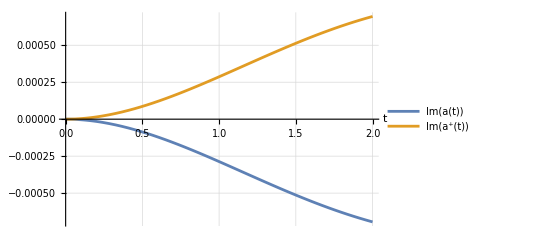

```mathematica
Plot[{Im[Evaluate[am[t]/.ans]],Im[Evaluate[ap[t]/.ans]](*,Im[Evaluate[ap[t]/.ans]]+Im[Evaluate[am[t]/.ans]]*)},{t,0,2},PlotLegends->Placed[{"Im(a(t))","Im(a^+(t))"},{Right,Top}],GridLines->Automatic,AxesLabel->Automatic]
```

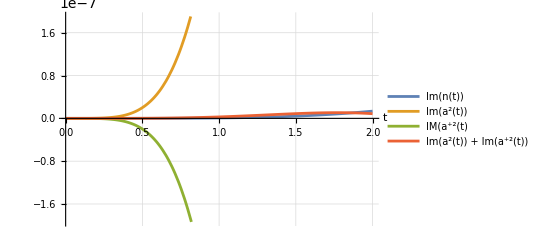

```mathematica
Plot[{Im[Evaluate[n[t]/.ans]],Im[Evaluate[am2[t]/.ans]],Im[Evaluate[ap2[t]/.ans]],Im[Evaluate[am2[t]/.ans]]+Im[Evaluate[ap2[t]/.ans]]},{t,0,2},PlotLegends->Placed[{"Im(n(t))","Im(a^2(t))","IM(a^(+2)(t)","Im(a^2(t)) + Im(a^(+2)(t))"},{Left,Top}],GridLines->Automatic,AxesLabel->Automatic,PlotRange->Automatic]
```

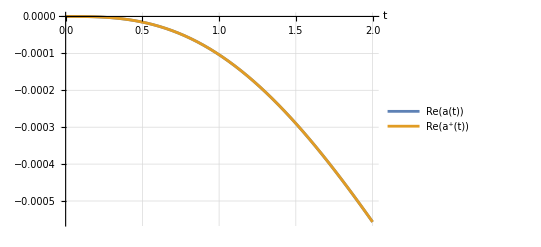

```mathematica
Plot[{Re[Evaluate[am[t]/.ans]],Re[Evaluate[ap[t]/.ans]]},{t,0,2},PlotLegends->Placed[{"Re(a(t))","Re(a^+(t))"},{Left,Bottom}],GridLines->Automatic,AxesLabel->Automatic]
```

# Переход в Шредингера

```mathematica
(*ca=({{Evaluate[am2[t]/.ans]-(Evaluate[am[t]/.ans])^2, 1/2+Evaluate[n[t]/.ans]-Evaluate[am[t]/.ans]Evaluate[ap[t]/.ans]}, {1/2+Evaluate[n[t]/.ans]-Evaluate[am[t]/.ans]Evaluate[ap[t]/.ans], Evaluate[ap2[t]/.ans]-(Evaluate[ap[t]/.ans])^2}});(*матрица ковариаций*)*)
mm[t_]:=({{(Evaluate[am[t]/.ans])[[1]]}, {(Evaluate[ap[t]/.ans])[[1]]}});(*Вектор средних*)
ca=({{(Evaluate[am2[t]/.ans]-(mm[t][[1,1]])^2)[[1]], (1/2+Evaluate[n[t]/.ans]-mm[t][[1,1]]mm[t][[2,1]])[[1]]}, {(1/2+Evaluate[n[t]/.ans]-mm[t][[1,1]]mm[t][[2,1]])[[1]], (Evaluate[ap2[t]/.ans]-(mm[t][[2,1]])^2)[[1]]}});(*Матрица ковариаций*)
h={{0,-Δ},{-Δ,0}}; (*матрица гамильтониана*)
g={{0,γ/2},{0,0}};(*матрица диссипаций*)
j=({{0, -1}, {1, 0}});
i=IdentityMatrix[2];
f={{ⅈ F},{-ⅈ F}};
mt[t_]:=MatrixExp[j.(ⅈ h+(Transpose[g]-g)/2)t].mm[t]+ⅈ(MatrixExp[j.(ⅈ h+(Transpose[g]-g)/2)t]-i).Inverse[j.(ⅈ h+(Transpose[g]-g)/2)].j.f;(*Вектор средних в Шредингере*)
ct[t_]:=MatrixExp[j.(ⅈ h+(Transpose[g]-g)/2)t].ca.MatrixExp[(-ⅈ h+(Transpose[g]-g)/2).j t]+∫_0^t MatrixExp[j.(ⅈ h+(Transpose[g]-g)/2)s].j.((g+Transpose[g])/2).j.MatrixExp[(-ⅈ h+(Transpose[g]-g)/2).j s]ⅆs(*Матрица ковариаций в Шредингере*)
```

```mathematica
ams[t_]:=mt[t][[1,1]];
aps[t_]:=mt[t][[2,1]];
ns[t_]:=ct[t][[1,2]]-1/2+ams[t]aps[t];
am2s[t_]:=ct[t][[1,1]]+ams[t]^2;
ap2s[t_]:=ct[t][[2,2]]+aps[t]^2;
```

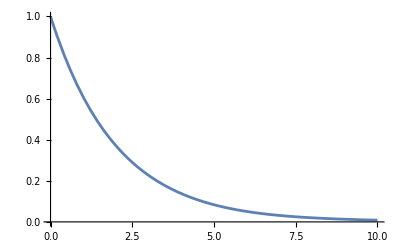

```mathematica
Plot[Re[ns[t]],{t,0,10}]
```

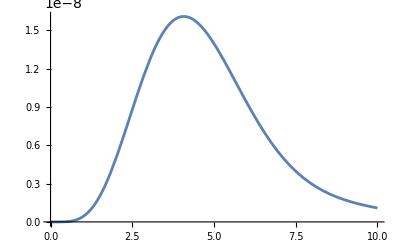

```mathematica
Plot[Im[ns[t]],{t,0,10}]
```

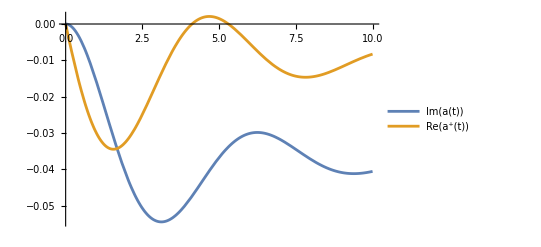

```mathematica
Plot[{Im[ams[t]],Re[aps[t]]},{t,0,10},PlotLegends->Placed[{"Im(a(t))","Re(a^+(t))"},{Left,Bottom}]]
```

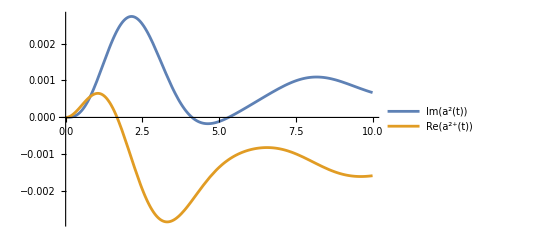

```mathematica
Plot[{Im[am2s[t]],Re[ap2s[t]]},{t,0,10},PlotLegends->Placed[{"Im(a^2(t))","Re(a^(2+)(t))"},{Left,Bottom}]]
```

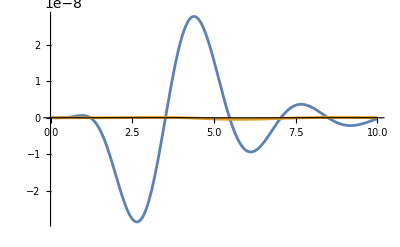

```mathematica
Plot[{Im[am2s[t]]+Im[ap2s[t]],Im[ams[t]]+Im[aps[t]]},{t,0,10},PlotRange->All]
```

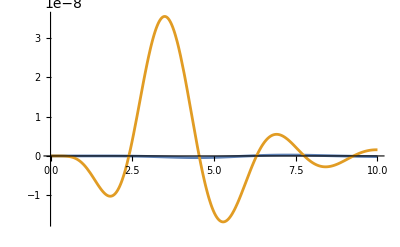

```mathematica
Plot[{Re[ams[t]]-Re[aps[t]],Re[am2s[t]]-Re[ap2s[t]]},{t,0,10},PlotRange->All]
```